## Definitions and setup

```mathematica
wd =SetDirectory@NotebookDirectory[];
```

```mathematica
states = {"Υ(1S)","Υ(2S)","χ_b(1P)","Υ(3S)","χ_b(2P)","Υ_2(1D)"};
tickSpecification=Table[{i,states[[i]]},{i,1,6}];
```

```mathematica
mapPoint[x_] := Around[x[[1]],x[[2]]]
```

```mathematica
ImportData[dir_]:=Module[{mean,stderr},
Clear[data];
data=Import[wd<>"/../"<>dir<>"/ratios.tsv"];
Print["Processing ",Length[data]," trajectories"];
mean=Mean[data];
stderr=StandardDeviation[data]/Sqrt[Length[data]];
mapPoint/@Transpose[{mean,stderr}]
]
```

## Plot setup

```mathematica
SetOptions[Plot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListPlot,Frame->True,Axes->False,ImageSize->500,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

## Peek at the data

```mathematica
raaData=ImportData["output"]
```

Processing 24 trajectories

{0.9670.033,0.960.04,0,0.960.04,0,0,0.410.06,0}

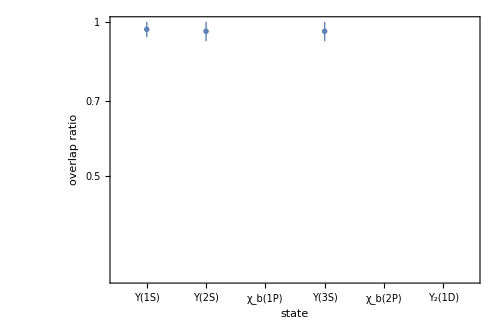

```mathematica
ListLogPlot[{raaData},ImageSize->500,PlotMarkers->{"OpenMarkers",7},Frame->True,FrameStyle->AbsoluteThickness[1],BaseStyle->16,AspectRatio->0.67,FrameLabel->{"state","overlap ratio"},PlotRange->{{0.5,6.5},All},FrameTicks->{{Automatic,Automatic},{tickSpecification,Automatic}}]
```